## Reference implementation for calculating points on the collision contour (manifold), for the next-nearest neighbor model

### General definitions

#### Dispersion relation

```mathematica
(* next-nearest neighbor dispersion relation; obtain nearest neighbor case by setting η=0 *)
ω[k_,η_]:=1-Cos[2π k]-η Cos[4π k]
```

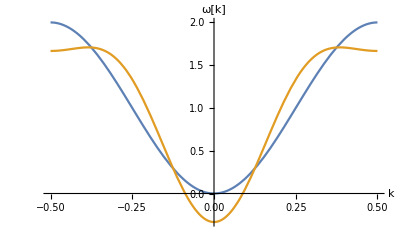

```mathematica
Plot[{ω[k,0],ω[k,1/3]},{k,-1/2,1/2},AxesLabel->{"k","ω[k]"}]
```

#### Factorization of the energy difference

```mathematica
(* reference implementation *)
EnergyDifference[k1_,k2_,k3_,k4_,η_]:=ω[k1,η]+ω[k2,η]-ω[k3,η]-ω[k4,η]
```

```mathematica
Econtour[s12_,Δ12_,Δ34_,η_]:=Cos[π s12]+2 η Cos[2 π s12](Cos[2 π Δ12]+Cos[2 π Δ34])
```

```mathematica
Etriv[Δ12_,Δ34_]:=4 Sin[π (Δ12+Δ34)]Sin[π(Δ12-Δ34)]
```

```mathematica
FullSimplify[Solve[{k3+k4==s34,1/2(k3-k4)==Δ34},{k3,k4}]]
```

{{k3→s34/2+Δ34,k4→1/2 (s34-2 Δ34)}}

```mathematica
(* check *)
FullSimplify[EnergyDifference[1/2 s12+Δ12,1/2 s12-Δ12,1/2 s12+Δ34,1/2 s12-Δ34,η]-Econtour[s12,Δ12,Δ34,η]Etriv[Δ12,Δ34]]
```

0

#### Derivative of the energy difference with respect to s_12

```mathematica
(* derivative of 'Econtour' with respect to Subscript[s, 12] *)
dEcontour[s12_,Δ12_,Δ34_,η_]:=-π Sin[π s12]-4 π η Sin[2 π s12](Cos[2 π Δ12]+Cos[2 π Δ34])
```

```mathematica
(* check *)
FullSimplify[D[Econtour[s12,Δ12,Δ34,η],s12]-dEcontour[s12,Δ12,Δ34,η]]
(* 'Etriv' is independent of Subscript[s, 12] *)
FullSimplify[D[Econtour[s12,Δ12,Δ34,η]Etriv[Δ12,Δ34],s12]-dEcontour[s12,Δ12,Δ34,η]Etriv[Δ12,Δ34]]
```

0

0

#### Calculation of s_12

```mathematica
CalculateSum12Diag[Δ12_,Δ34_,η_]:=Module[{t=4η(Cos[2 π Δ12]+Cos[2 π Δ34])},1/π ArcCos[If[t==0,0,(√(1+2 t^2)-1)/(2 t)]]]
```

```mathematica
CalculateSum12Ellipsoid[Δ12_,Δ34_,η_]:=Module[{t=4η(Cos[2 π Δ12]+Cos[2 π Δ34])},1/π ArcCos[-(1+√(1+2 t^2))/(2t)]]
```

```mathematica
VerifySum12EllipsoidParams[Δ12_,Δ34_,η_]:=η Abs[Cos[2 π Δ12]+Cos[2 π Δ34]]≥1/2
```

```mathematica
(* check *)
FullSimplify[Econtour[CalculateSum12Diag[Δ12,Δ34,η],Δ12,Δ34,η],Assumptions->{η>0}]
FullSimplify[Econtour[CalculateSum12Ellipsoid[Δ12,Δ34,η],Δ12,Δ34,η],Assumptions->{η>0}]
```

0

0

```mathematica
(* special case η=0 *)
CalculateSum12Diag[Δ12,Δ34,0(*η*)]
```

1/2

### Numerical examples

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* uniform grid *)
Subscript[Δ, list]=Block[{gridsize=128},Range[-1/2,1/2-1/gridsize,1/gridsize]];
```

```mathematica
(* mollification parameter *)
Subscript[ϵ, val]=1/2;
```

#### “Diagonal” contour

```mathematica
(* points on the contour *)
Subscript[pts, contour,diag]=Block[{η=1/3,s12},Flatten[Outer[Mod[N[{1/2 s12+#1,1/2 s12-#1,1/2 s12+#2,1/2 s12-#2}/.{s12->CalculateSum12Diag[#1,#2,η]}],1]&,Subscript[Δ, list],Subscript[Δ, list]],1]];
Dimensions[%]
```

{16384,4}

```mathematica
(* derivative of the energy difference with respect to Subscript[s, 12] *)
Subscript[dω, contour,diag]=Block[{η=1/3,s12},Flatten[Outer[N[dEcontour[s12,#1,#2,η]Etriv[#1,#2]/.{s12->CalculateSum12Diag[#1,#2,η]}]&,Subscript[Δ, list],Subscript[Δ, list]],1]];
Dimensions[%]
```

{16384}

```mathematica
(* sort points *)
Ordering[Subscript[pts, contour,diag],Length[Subscript[pts, contour,diag]],#1⟦1⟧<#2⟦1⟧∨(#1⟦1⟧==#2⟦1⟧∧#1⟦3⟧<#2⟦3⟧)&];
{Subscript[pts, contour,diag]=Subscript[pts, contour,diag]⟦%⟧,Subscript[dω, contour,diag]=Subscript[dω, contour,diag]⟦%⟧};
```

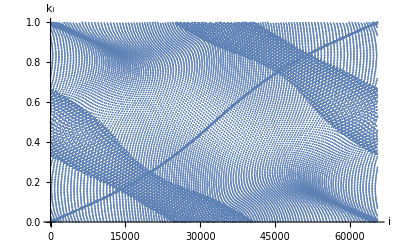

```mathematica
ListPlot[Flatten[Subscript[pts, contour,diag]],AxesLabel->{"i","k_i"}]
```

```mathematica
Subscript[k, list,diag]=Union[Flatten[Subscript[pts, contour,diag]],SameTest->(Abs[#1-#2]<10^-12&)];
Dimensions[%]
```

{8320}

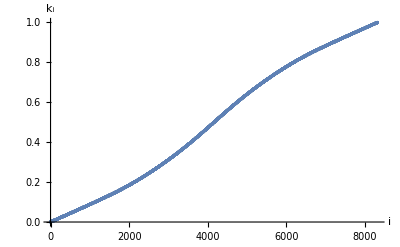

```mathematica
ListPlot[Subscript[k, list,diag],AxesLabel->{"i","k_i"}]
```

```mathematica
(* mollified inverse of dω *)
Subscript[invdω, contour,diag]=π(#^2+Subscript[ϵ, val]^2)^(-1/2)&/@Subscript[dω, contour,diag];
Dimensions[%]
```

{16384}

```mathematica
(* save as reference to disk *)
Subscript[fn, base]="collision_contour_ref/nnn_diag";
Export[Subscript[fn, base]<>"_klist_ref.dat",Subscript[k, list,diag],"Real64"];
Export[Subscript[fn, base]<>"_contour_k4_ref.dat",Flatten[Subscript[pts, contour,diag]],"Real64"];
Export[Subscript[fn, base]<>"_idomega_ref.dat",Subscript[invdω, contour,diag],"Real64"];
```

#### “Ellipsoid” contour

```mathematica
(* select admissible points *)
Block[{η=1/3},Subscript[Δ2, list,ellipsoid]=Select[Flatten[Outer[{##}&,Subscript[Δ, list],Subscript[Δ, list]],1],VerifySum12EllipsoidParams[First[#],Last[#],η]&]];
Dimensions[%]
```

{2794,2}

```mathematica
(* points on the contour *)
Block[{η=1/3,s12},Subscript[pts, contour,ellipsoid]=Mod[N[{1/2 s12+#1,1/2 s12-#1,1/2 s12+#2,1/2 s12-#2}/.{s12->CalculateSum12Ellipsoid[#1,#2,η]}],1]&@@#&/@Subscript[Δ2, list,ellipsoid]];
Dimensions[%]
```

{2794,4}

```mathematica
(* derivative of the energy difference with respect to Subscript[s, 12] *)
Subscript[dω, contour,ellipsoid]=Block[{η=1/3,s12},N[dEcontour[s12,#1,#2,η]Etriv[#1,#2]/.{s12->CalculateSum12Ellipsoid[#1,#2,η]}]&@@#&/@Subscript[Δ2, list,ellipsoid]];
Dimensions[%]
```

{2794}

```mathematica
(* sort points *)
Ordering[Subscript[pts, contour,ellipsoid],Length[Subscript[pts, contour,ellipsoid]],#1⟦1⟧<#2⟦1⟧∨(#1⟦1⟧==#2⟦1⟧∧#1⟦3⟧<#2⟦3⟧)&];
{Subscript[pts, contour,ellipsoid]=Subscript[pts, contour,ellipsoid]⟦%⟧,Subscript[dω, contour,ellipsoid]=Subscript[dω, contour,ellipsoid]⟦%⟧};
```

```mathematica
(* visualize points on contour *)
ListPointPlot3D[{#⟦1⟧,#⟦3⟧,#⟦4⟧}&/@Subscript[pts, contour,ellipsoid],AxesLabel->{"k_1","k_3","k_4"}]
```

-Graphics3D-

```mathematica
Subscript[k, list,ellipsoid]=Union[Flatten[Subscript[pts, contour,ellipsoid]],SameTest->(Abs[#1-#2]<10^-12&)];
Dimensions[%]
```

{1440}

```mathematica
(* mollified inverse of dω *)
Subscript[invdω, contour,ellipsoid]=π(#^2+Subscript[ϵ, val]^2)^(-1/2)&/@Subscript[dω, contour,ellipsoid];
Dimensions[%]
```

{2794}

```mathematica
(* save as reference to disk *)
Subscript[fn, base]="collision_contour_ref/nnn_ellipsoid";
Export[Subscript[fn, base]<>"_klist_ref.dat",Subscript[k, list,ellipsoid],"Real64"];
Export[Subscript[fn, base]<>"_contour_k4_ref.dat",Flatten[Subscript[pts, contour,ellipsoid]],"Real64"];
Export[Subscript[fn, base]<>"_idomega_ref.dat",Subscript[invdω, contour,ellipsoid],"Real64"];
```